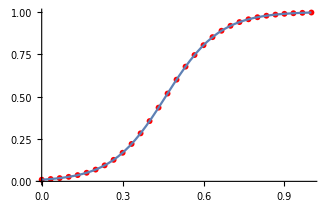
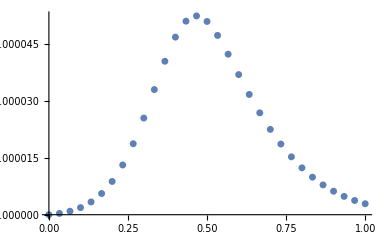
GraphicRow[{-Graphics-,-Graphics-}]

```mathematica
logisticExact[t_]:=0.01/(0.01+0.99E^(-10t))
f[y_]:=(10y(1-y));

RK4[f_,y0_,n_,T_] := (
Block[{k1,k2,k3,k4,y,h,i},
h = N[T/n];
y = Table[0,n+1];
y[[1]] = y0;
For[i=1,i<=n,++i,
k1 = h f[y[[i]]];
k2 = h f[y[[i]]+0.5 k1];
k3 = h f [y[[i]]+ 0.5 k2];
k4 = h f[y[[i]]+k3];
y[[i+1]] = y[[i]] + 1.0/6.0(k1 + 2k2 + 2k3 + k4);
];
Table[{h * (i-1),y[[i]]},{i,1,Length[y]}]
]
);

sol30Nodes = RK4[f,0.01,30,1];
sol30NodesError = Table[{sol30Nodes[[i,1]],Abs[logisticExact[sol30Nodes[[i,1]]]-sol30Nodes[[i,2]]]}, {i,1,Length[sol30Nodes]}];
GraphicRow[
{Show[{
ListPlot[sol30Nodes,PlotStyle->Red],
Plot[logisticExact[t],{t,0,1}]
}],
ListPlot[sol30NodesError]
}]
```

Part::partd: Part specification RK23[f2,1,0,10,0.1,1/100000]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification RK23[f2,1,0,10,0.1,1/100000]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification RK23[f2,1,0,10,0.1,1/100000]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification RK23[f2,1,0,10,0.1,1/100000]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: RK23[f2,1.,0.,10.,0.1,0.00001] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[RK23[f2,1,0,10,0.1,1/100000],PlotStyle→RGBColor[1, 0, 0]],}].

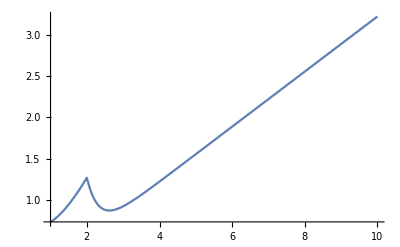
Show[{ListPlot[RK23[f2,1,0,10,0.1,1/100000],PlotStyle→RGBColor[1, 0, 0]],-Graphics-}]

Part::partd: Part specification RK23[f2,1.,0,10.,0.1,0.00001]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification RK23[f2,1.,0.,10.,0.1,0.00001]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification RK23[f2,1.,0,10.,0.1,0.00001]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification RK23[f2,1.,0,10.,0.1,0.00001]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
ClearAll[f];
b[t_]:=If[0≤t≤2,1,3];
f2[t_,y_]:=-b[t]y+t;
f2Exact[t_]:=If[0≤t≤2,t-1+2E^(-t),t/3-1/9+E^(-3t)((4/9)E^6+2E^4)]

RK23[f_,y0_,t0_,T,h0_,tol_] := (
Block[{y,c,t,h=h0,i=1,k1,k2,k3,err},
t = {t0};
y = {y0};
While[t[[i]]<T,
k1=h f[t[[i]],y[[i]]];
	k2=h f[t[[i]]+h,y[[i]]+k1];
	k3=h f[t[[i]]+h/2,y[[i]]+0.25k1+0.25k2];
	err=Abs[(k1+k2-2k3)/3];
While[err>tol,
	h=h(tol/(err))^(1/3);
	k1=h f[t[[i]],y[[i]]];
	k2=h f[t[[i]]+h,y[[i]]+k1];
	k3=h f[t[[i]]+h/2,y[[i]]+0.25k1+0.25k2];
	err=Abs[(k1+k2-2k3)/3];
	];
AppendTo[y,y[[i]]+(1/6)k1+(1/6)k2+(2/3)k3];
AppendTo[t,t[[i]]+h];
++i;
err=Abs[(k1+k2-2k3)/3];
	 h=h(tol/(err))^(1/3);
];
Table[{t[[i]],y[[i]]},{i,1,Length[y]}]
]
);

RK23sol=RK23[f2,1,0,10,0.1,10^-5];
RK23error=Table[{RK23sol[[i,1]],Abs[f2Exact[RK23sol[[i,1]]]-RK23sol[[i,2]]]},{i,1,Length[RK23sol]}];
RK23step=Table[{RK23sol[[i,1]],Abs[RK23sol[[i,1]]-RK23sol[[i+1,1]]]},{i,1,Length[RK23sol]-1}];
Print[Show[{ListPlot[RK23sol,PlotStyle->Red],Plot[f2Exact[t],{t,1,10}]}]];
Print[ListPlot[RK23error,PlotRange->All]];
Print[ListPlot[RK23step,PlotRange->All]];
```